# 4Body Level Spacing Analysis

```mathematica
PBrody[x_,w_]:=(1+w)(Gamma[(2+w)/(1+w)])^(1+w)x^w Exp[-(Gamma[(2+w)/(1+w)]x)^(1+w)];
```

```mathematica
bins=Table[x,{x,0,5,0.2}];
bFit=Table[0.5*(bins[[i]]+bins[[i+1]]),{i,1,Length[bins]-1}];
```

Make a module to do everything above and output what we want

```mathematica
Analyze[MyPath_,Ewindowsize_,bins_,bFit_,Parfile_]:=Module[{rundata0,DD,curvestemp0,Curves0,Evals0,Ecutoff0,eValsBound0,Es0,eTrim0,avg0,ρ0,EspaceBin0,NormBrodyBinCs0,Brodyw,BrodyError,brodyPdist0,pfit0,pbrody,w,SampleRange,BrodyDistribution,x,phist0,NumSpacings,pcurves0,penergies0,pcurvesenergies,DeepStatesRange,eValsDeep0,pdeepstates0,Ewindownew,Ethresh,wfnkeep},
BrodyDistribution=ProbabilityDistribution[PBrody[x,w],{x,0,∞},Assumptions->w>0];
rundata0=Import[StringJoin[MyPath,Parfile],"list"];
DD=Interpreter["Number"][StringReplace[StringSplit[rundata0[[8]]],"d"->""]][[1]];
curvestemp0=Transpose[Import[StringJoin[MyPath,"AdiabaticCurves.dat"]]];
Curves0=Table[Table[{curvestemp0[[1,i]],curvestemp0[[j,i]]},{i,1,Length[curvestemp0[[1]]]}],{j,2,Length[curvestemp0]}];
Evals0=Flatten[Import[StringJoin[MyPath,"Eigenvals.dat"]]];
Ethresh=Evals0[[4]];
Ecutoff0=Evals0[[4]];
Evals0=Sort[Drop[Evals0,1;;4]];
(*Ewindownew=0.1 (Ecutoff0-Evals0[[1]]);*)
Ecutoff0=-2.7DD;
SampleRange=Ecutoff0-(Ewindowsize)/2.0<#<Ecutoff0+Ewindowsize/2.0&;
wfnkeep = Length[Select[Evals0,#<Ecutoff0&]];
DeepStatesRange=#<Ecutoff0-Ewindowsize&;
eValsBound0 = Sort[Select[Evals0,SampleRange]];
eValsDeep0=Complement[Evals0,eValsBound0];
eValsDeep0=Sort[Select[eValsDeep0,#<Ethresh&]];
(*eValsDeep0=Sort[Select[Evals0,DeepStatesRange]];*)
pcurves0=ListPlot[Curves0,FrameLabel->{"R","Energy"},PlotTheme->None,PlotStyle->{{Blue,Thickness[0.002],Opacity[0.5]}},PlotMarkers->None,Joined->True,PlotRange->{1.05Min[curvestemp0[[2]]],Ecutoff0+100}];
penergies0=ListPlot[Table[{8,eValsBound0[[i]]},{i,1,Length[eValsBound0]}],PlotMarkers->Graphics[{Thickness[.001],Black,Line[{{1.5,0},{2,0}}]}]];
pdeepstates0=ListPlot[Table[{8,eValsDeep0[[i]]},{i,1,Length[eValsDeep0]}],PlotMarkers->Graphics[{Thickness[.001],Red,Line[{{1.5,0},{2,0}}]}]];
pcurvesenergies=Show[pcurves0,penergies0,pdeepstates0,Frame->True];
Es0=Table[eValsBound0[[i+1]]-eValsBound0[[i]],{i,1,Length[eValsBound0]-1}];
eTrim0= Select[Es0,#>0.000001&];
NumSpacings=Length[eTrim0];
avg0 = Mean[eTrim0];
eTrim0 = eTrim0/avg0;
ρ0=1/avg0;
EspaceBin0=BinCounts[eTrim0,{bins}];
NormBrodyBinCs0=Table[EspaceBin0[[i]]/Total[EspaceBin0]/(bins[[i+1]]-bins[[i]]),{i,1,Length[bins]-1}];
Brodyw=w/.FindDistributionParameters[eTrim0,BrodyDistribution];
BrodyError=√(-1/D[LogLikelihood[BrodyDistribution,eTrim0],{w,2}])/.w->Brodyw;
brodyPdist0 = Table[{bFit[[i]],NormBrodyBinCs0[[i]]},{i,1,Length[bFit]}];
phist0=ListPlot[brodyPdist0,InterpolationOrder->0,Joined->True,PlotRange->All,PlotStyle->Black,PlotMarkers->None];
(*pars0 = FindFit[brodyPdist0,{PBrody[s,w],w>0,w<1},{w},s]*)
pfit0=Plot[PBrody[s,Brodyw],{s,0,5},PlotRange->All,PlotStyle->Red];
pbrody=Show[phist0,pfit0,FrameLabel->{"s / s̄","P(s)"},Frame-> True,LabelStyle->Medium,Epilog->{Text[Style["w = ",Medium],{2.5,0.6}],Text[Style[DecimalForm[Brodyw,{2,2}]±DecimalForm[BrodyError,{2,2}],Medium],{3.9,0.6}]}];
{DD,NumSpacings,ρ0,Brodyw,BrodyError,pcurvesenergies,pbrody,Ecutoff0,wfnkeep}

]
```

```mathematica
Ewindowsize=10;
```

```mathematica
V40SVDPaths= {"/Users/niravmehta/Documents/GitHub/4BodySVD/runs40/run1/",
"/Users/niravmehta/Documents/GitHub/4BodySVD/runs40/run2/",
"/Users/niravmehta/Documents/GitHub/4BodySVD/runs40/run3/",
"/Users/niravmehta/Documents/GitHub/4BodySVD/runs40/run4/"};
```

```mathematica
V100SVDPaths= {"/Users/niravmehta/Documents/GitHub/4BodySVD/runs100/run1/",
"/Users/niravmehta/Documents/GitHub/4BodySVD/runs100/run2/",
"/Users/niravmehta/Documents/GitHub/4BodySVD/runs100/run3/",
"/Users/niravmehta/Documents/GitHub/4BodySVD/runs100/run4/"};
```

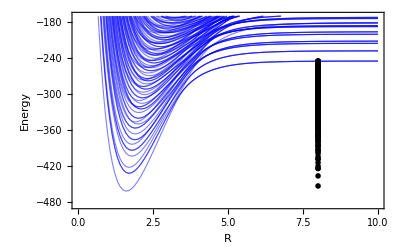
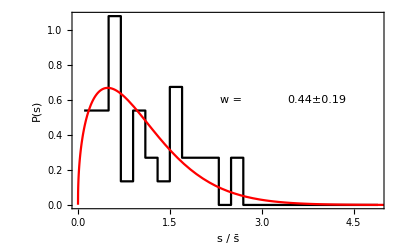
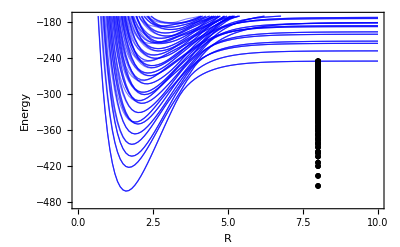
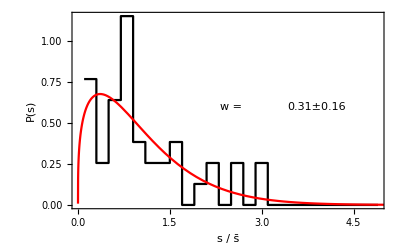
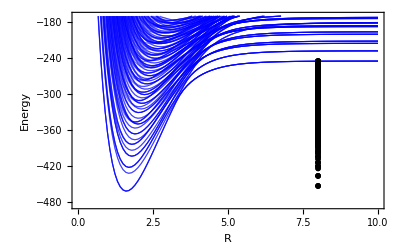
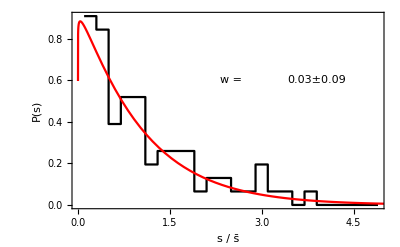
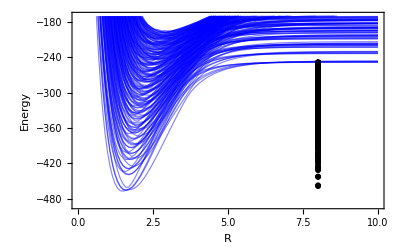
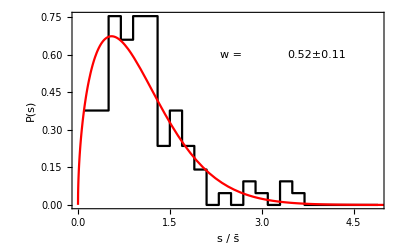
{{100.,37,3.75385,0.44295,0.189263,-Graphics-,-Graphics-,-270.,211},{100.,39,4.00806,0.311053,0.162884,-Graphics-,-Graphics-,-270.,258},{100.,77,7.79073,0.0332588,0.0940751,-Graphics-,-Graphics-,-270.,469},{100.,106,10.6483,0.520461,0.109362,-Graphics-,-Graphics-,-270.,623}}

```mathematica
V100SVDData=Table[Analyze[V100SVDPaths[[i]],Ewindowsize,bins,bFit,"4BodySVD.par"],{i,1,Length[V100SVDPaths]}]
```

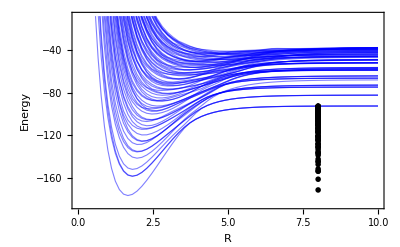
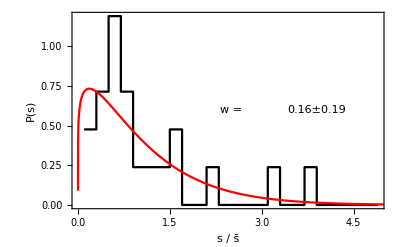
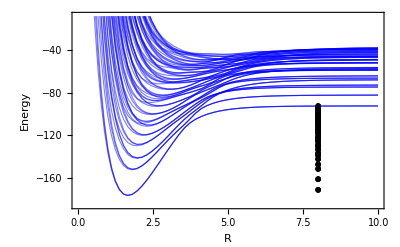
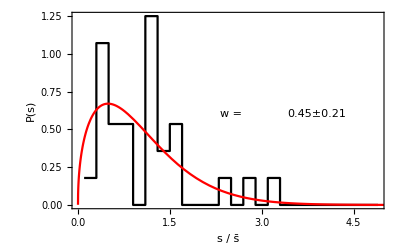
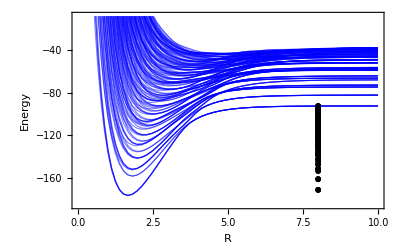
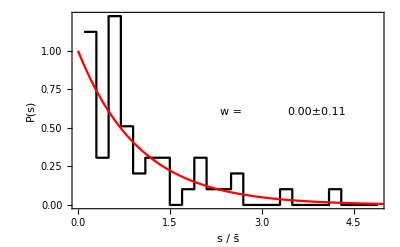
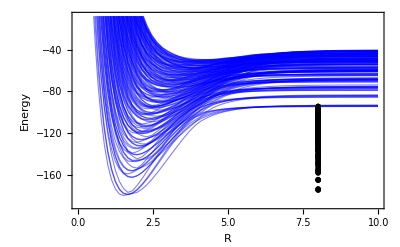
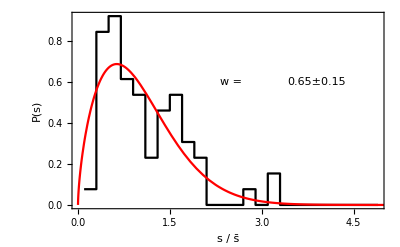
{{40.,21,2.20855,0.155108,0.187644,-Graphics-,-Graphics-,-108.,49},{40.,28,2.95115,0.448389,0.207569,-Graphics-,-Graphics-,-108.,69},{40.,50,5.25814,2.94862×10^-9,0.107341,-Graphics-,-Graphics-,-108.,118},{40.,65,6.68791,0.645865,0.148214,-Graphics-,-Graphics-,-108.,158}}

```mathematica
V40SVDData=Table[Analyze[V40SVDPaths[[i]],Ewindowsize,bins,bFit,"4BodySVD.par"],{i,1,Length[V40SVDPaths]}]
```

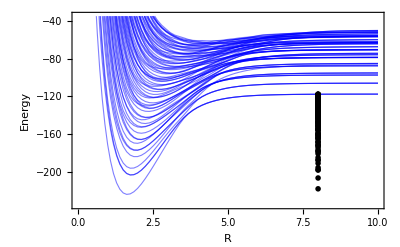
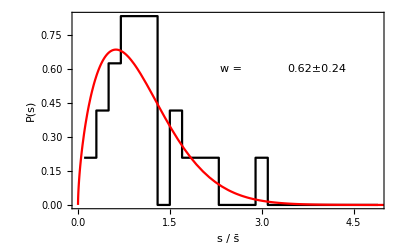
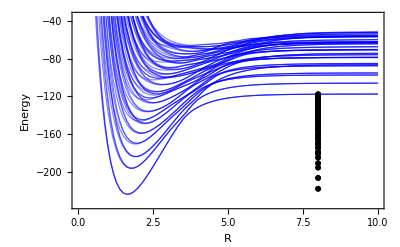
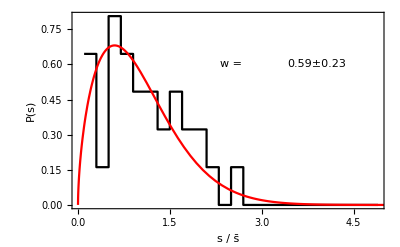
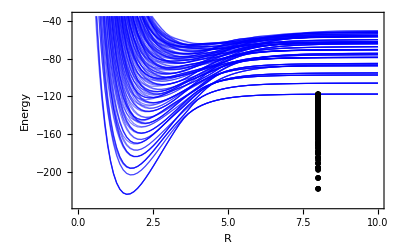
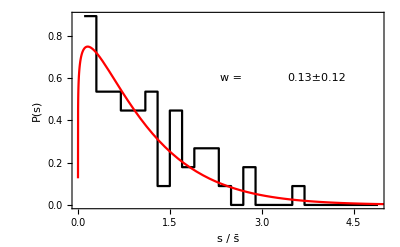
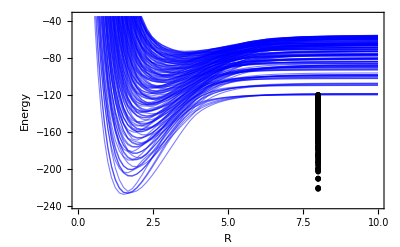
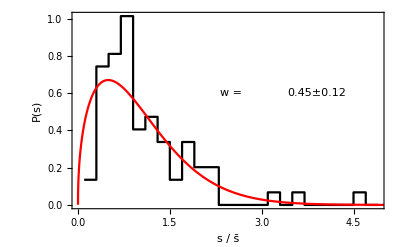
{{50.,24,2.49982,0.623364,0.244249,-Graphics-,-Graphics-,-135.,71},{50.,31,3.16013,0.590205,0.227724,-Graphics-,-Graphics-,-135.,95},{50.,56,5.70862,0.133321,0.123992,-Graphics-,-Graphics-,-135.,166},{50.,74,7.44403,0.452735,0.119325,-Graphics-,-Graphics-,-135.,222}}

```mathematica
V50Paths= {"/Users/niravmehta/Documents/GitHub/4BodySVD/runs50/run1/",
"/Users/niravmehta/Documents/GitHub/4BodySVD/runs50/run2/",
"/Users/niravmehta/Documents/GitHub/4BodySVD/runs50/run3/",
"/Users/niravmehta/Documents/GitHub/4BodySVD/runs50/run4/"};
V50Data=Table[Analyze[V50Paths[[i]],Ewindowsize,bins,bFit,"4BodySVD.par"],{i,1,Length[V50Paths]}]
```

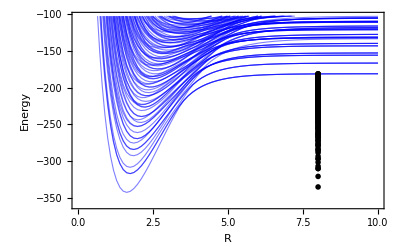
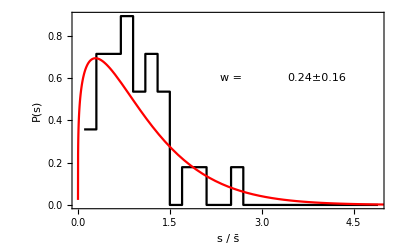
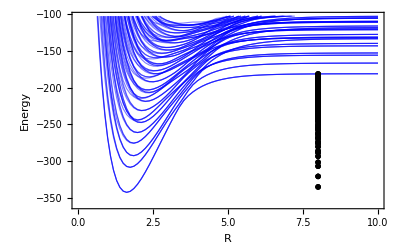
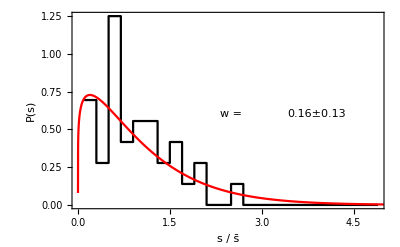
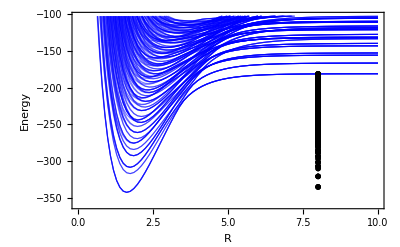
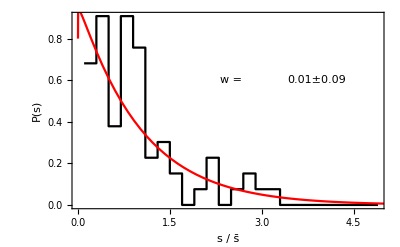
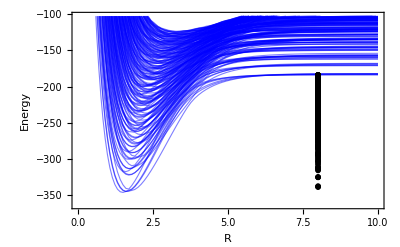
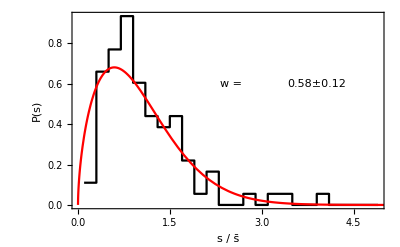
{{75.,29,3.27736,0.240381,0.157751,-Graphics-,-Graphics-,-202.5,132},{75.,37,4.12179,0.163125,0.132698,-Graphics-,-Graphics-,-202.5,168},{75.,67,7.46379,0.0143147,0.0880628,-Graphics-,-Graphics-,-202.5,300},{75.,91,9.28638,0.583621,0.117226,-Graphics-,-Graphics-,-202.5,409}}

```mathematica
Ewindowsize=10;
V75Paths= {"/Users/niravmehta/Documents/GitHub/4BodySVD/runs75/run1/",
"/Users/niravmehta/Documents/GitHub/4BodySVD/runs75/run2/",
"/Users/niravmehta/Documents/GitHub/4BodySVD/runs75/run3/",
"/Users/niravmehta/Documents/GitHub/4BodySVD/runs75/run4/"};
V75Data=Table[Analyze[V75Paths[[i]],Ewindowsize,bins,bFit,"4BodySVD.par"],{i,1,Length[V75Paths]}]
```

```mathematica
SVDType1Paths={"/Users/niravmehta/Documents/GitHub/4BodySVD/runs20/run1/",
"/Users/niravmehta/Documents/GitHub/4BodySVD/runs30/run1/",
"/Users/niravmehta/Documents/GitHub/4BodySVD/runs40/run1/",
"/Users/niravmehta/Documents/GitHub/4BodySVD/runs50/run1/",
"/Users/niravmehta/Documents/GitHub/4BodySVD/runs75/run1/",
"/Users/niravmehta/Documents/GitHub/4BodySVD/runs100/run1/"};
SVDType2Paths={"/Users/niravmehta/Documents/GitHub/4BodySVD/runs20/run2/",
"/Users/niravmehta/Documents/GitHub/4BodySVD/runs30/run2/",
"/Users/niravmehta/Documents/GitHub/4BodySVD/runs40/run2/",
"/Users/niravmehta/Documents/GitHub/4BodySVD/runs50/run2/",
"/Users/niravmehta/Documents/GitHub/4BodySVD/runs75/run2/",
"/Users/niravmehta/Documents/GitHub/4BodySVD/runs100/run2/"};
SVDType3Paths={"/Users/niravmehta/Documents/GitHub/4BodySVD/runs20/run3/",
"/Users/niravmehta/Documents/GitHub/4BodySVD/runs30/run3/",
"/Users/niravmehta/Documents/GitHub/4BodySVD/runs40/run3/",
"/Users/niravmehta/Documents/GitHub/4BodySVD/runs50/run3/",
"/Users/niravmehta/Documents/GitHub/4BodySVD/runs75/run3/",
"/Users/niravmehta/Documents/GitHub/4BodySVD/runs100/run3/"};
SVDType4Paths={"/Users/niravmehta/Documents/GitHub/4BodySVD/runs20/run4/",
"/Users/niravmehta/Documents/GitHub/4BodySVD/runs30/run4/",
"/Users/niravmehta/Documents/GitHub/4BodySVD/runs40/run4/",
"/Users/niravmehta/Documents/GitHub/4BodySVD/runs50/run4/",
"/Users/niravmehta/Documents/GitHub/4BodySVD/runs75/run4/",
"/Users/niravmehta/Documents/GitHub/4BodySVD/runs100/run4/"};
```

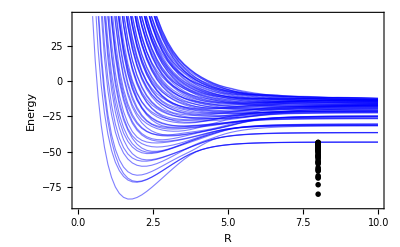
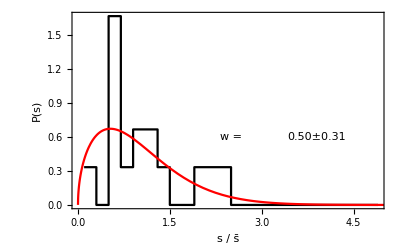
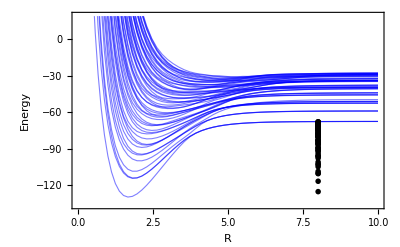
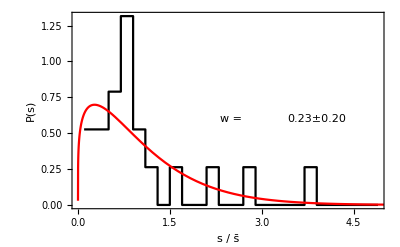
{{20.,15,1.56619,0.495424,0.31037,-Graphics-,-Graphics-,-54.,15},{30.,19,1.96141,0.226832,0.204792,-Graphics-,-Graphics-,-81.,30},{40.,21,2.20855,0.155108,0.187644,-Graphics-,-Graphics-,-108.,49},{50.,24,2.49982,0.623364,0.244249,-Graphics-,-Graphics-,-135.,71},{75.,29,3.27736,0.240381,0.157751,-Graphics-,-Graphics-,-202.5,132},{100.,37,3.75385,0.44295,0.189263,-Graphics-,-Graphics-,-270.,211}}

```mathematica
SVDType1Data=Table[Analyze[SVDType1Paths[[i]],Ewindowsize,bins,bFit,"4BodySVD.par"],{i,1,Length[SVDType1Paths]}]
```

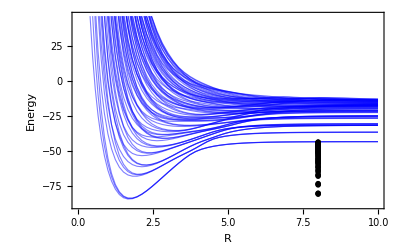
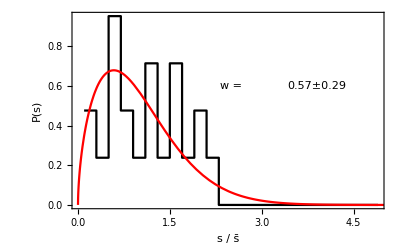
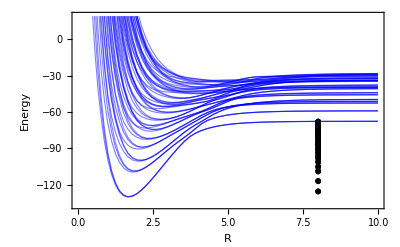
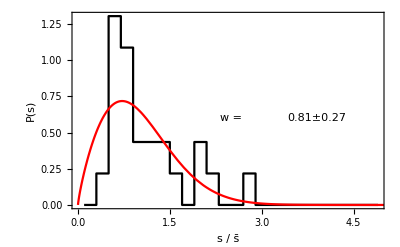
{{20.,21,2.17373,0.571746,0.287066,-Graphics-,-Graphics-,-54.,26},{30.,23,2.36727,0.809851,0.267177,-Graphics-,-Graphics-,-81.,44},{40.,28,2.95115,0.448389,0.207569,-Graphics-,-Graphics-,-108.,69},{50.,31,3.16013,0.590205,0.227724,-Graphics-,-Graphics-,-135.,95},{75.,37,4.12179,0.163125,0.132698,-Graphics-,-Graphics-,-202.5,168},{100.,39,4.00806,0.311053,0.162884,-Graphics-,-Graphics-,-270.,258}}

```mathematica
SVDType2Data=Table[Analyze[SVDType2Paths[[i]],Ewindowsize,bins,bFit,"4BodySVD.par"],{i,1,Length[SVDType2Paths]}]
```

```mathematica
SVDrhodat1=Table[{√SVDType1Data[[i,1]],SVDType1Data[[i,3]]},{i,1,Length[SVDType1Data]}]
```

{{4.47214,1.56619},{5.47723,1.96141},{6.32456,2.20855},{7.07107,2.49982},{8.66025,3.27736},{10.,3.75385}}

```mathematica
SVDQMdosline1=Fit[SVDrhodat1,{0,x},x]
```

0.+0.366073 x

```mathematica
SVDType2Data=Table[Analyze[SVDType2Paths[[i]],Ewindowsize,bins,bFit,"4BodySVD.par"],{i,1,Length[SVDType2Paths]}]
```

{{20.,21,2.17373,0.571746,0.287066,-Graphics-,-Graphics-,-54.,26},{30.,23,2.36727,0.809851,0.267177,-Graphics-,-Graphics-,-81.,44},{40.,28,2.95115,0.448389,0.207569,-Graphics-,-Graphics-,-108.,69},{50.,31,3.16013,0.590205,0.227724,-Graphics-,-Graphics-,-135.,95},{75.,37,4.12179,0.163125,0.132698,-Graphics-,-Graphics-,-202.5,168},{100.,39,4.00806,0.311053,0.162884,-Graphics-,-Graphics-,-270.,258}}

```mathematica
SVDrhodat2=Table[{√SVDType2Data[[i,1]],SVDType2Data[[i,3]]},{i,1,Length[SVDType2Data]}]
SVDQMdosline2=Fit[SVDrhodat2,{0,x},x]
```

{{4.47214,2.17373},{5.47723,2.36727},{6.32456,2.95115},{7.07107,3.16013},{8.66025,4.12179},{10.,4.00806}}

0.+0.442774 x

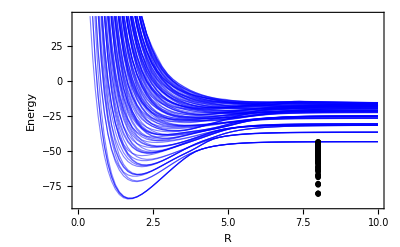
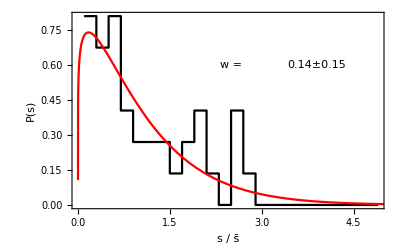
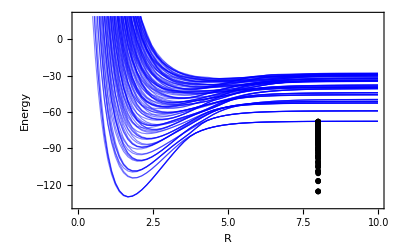
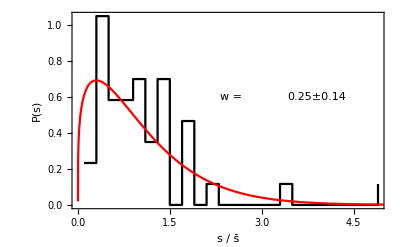
{{20.,37,3.81079,0.143762,0.151662,-Graphics-,-Graphics-,-54.,41},{30.,43,4.40179,0.252392,0.139321,-Graphics-,-Graphics-,-81.,74},{40.,50,5.25814,2.94862×10^-9,0.107341,-Graphics-,-Graphics-,-108.,118},{50.,56,5.70862,0.133321,0.123992,-Graphics-,-Graphics-,-135.,166},{75.,67,7.46379,0.0143147,0.0880628,-Graphics-,-Graphics-,-202.5,300},{100.,77,7.79073,0.0332588,0.0940751,-Graphics-,-Graphics-,-270.,469}}

```mathematica
SVDType3Data=Table[Analyze[SVDType3Paths[[i]],Ewindowsize,bins,bFit,"4BodySVD.par"],{i,1,Length[SVDType3Paths]}]
```

```mathematica
SVDrhodat3=Table[{√SVDType3Data[[i,1]],SVDType3Data[[i,3]]},{i,1,Length[SVDType3Data]}]
SVDQMdosline3=Fit[SVDrhodat3,{0,x},x]
```

{{4.47214,3.81079},{5.47723,4.40179},{6.32456,5.25814},{7.07107,5.70862},{8.66025,7.46379},{10.,7.79073}}

0.+0.816886 x

```mathematica
Ewindowsize=10;SVDType4Data=Table[Analyze[SVDType4Paths[[i]],Ewindowsize,bins,bFit,"4BodySVD.par"],{i,1,Length[SVDType4Paths]}]
```

{{20.,47,4.8003,0.564427,0.149026,-Graphics-,-Graphics-,-54.,55},{30.,58,6.04938,0.444852,0.134709,-Graphics-,-Graphics-,-81.,101},{40.,65,6.68791,0.645865,0.148214,-Graphics-,-Graphics-,-108.,158},{50.,74,7.44403,0.452735,0.119325,-Graphics-,-Graphics-,-135.,222},{75.,91,9.28638,0.583621,0.117226,-Graphics-,-Graphics-,-202.5,409},{100.,106,10.6483,0.520461,0.109362,-Graphics-,-Graphics-,-270.,623}}

```mathematica
run100type4data=Analyze["/Users/niravmehta/Documents/GitHub/4BodySVD/runs100/run4/",Ewindowsize,bins,bFit,"4BodySVD.par"]
```

{100.,106,10.6483,0.520461,0.109362,-Graphics-,-Graphics-,-270.,623}

```mathematica
Export["/Users/niravmehta/Documents/MyPapers/Molecules-Resubmit-Round1-2020/newfigs/SVDCurves.pdf",run100type4data[[6]]]
```

/Users/niravmehta/Documents/MyPapers/Molecules-Resubmit-Round1-2020/newfigs/SVDCurves.pdf

```mathematica
Export["/Users/niravmehta/Documents/MyPapers/Molecules-Resubmit-Round1-2020/newfigs/SVDBrodyDist100.pdf",run100type4data[[7]]]
```

/Users/niravmehta/Documents/MyPapers/Molecules-Resubmit-Round1-2020/newfigs/SVDBrodyDist100.pdf

```mathematica
Export["/Users/niravmehta/Documents/MyPapers/Molecules-Resubmit-Round1-2020/newfigs/SVDCurvesDist.pdf",Grid[{{run100type4data[[6]]},{run100type4data[[7]]}}]]
```

/Users/niravmehta/Documents/MyPapers/Molecules-Resubmit-Round1-2020/newfigs/SVDCurvesDist.pdf

```mathematica
Show[pbrody]
```

Show::gtype: Symbol is not a type of graphics.

Show[pbrody]

```mathematica
(*BrodyTable={Legended[Table[{SVDType3Data[[i,1]],SVDType3Data[[i,4]]±SVDType3Data[[i,5]]},{i,1,Length[SVDType3Data]}],"m_3=m_4=m_1=m_2"],
Legended[Table[{SVDType4Data[[i,1]],SVDType4Data[[i,4]]±SVDType4Data[[i,5]]},{i,1,Length[SVDType4Data]}],"m_3=m_4=3/2m_1=3/2m_2"]}*)
```

```mathematica
BrodyTable={Table[{SVDType3Data[[i,1]],SVDType3Data[[i,4]]±SVDType3Data[[i,5]]},{i,1,Length[SVDType3Data]}],
Table[{SVDType4Data[[i,1]],SVDType4Data[[i,4]]±SVDType4Data[[i,5]]},{i,1,Length[SVDType4Data]}]}
```

{{{20.,0.143762±0.151662},{30.,0.252392±0.139321},{40.,2.94862×10^-9±0.107341},{50.,0.133321±0.123992},{75.,0.0143147±0.0880628},{100.,0.0332588±0.0940751}},{{20.,0.564427±0.149026},{30.,0.444852±0.134709},{40.,0.645865±0.148214},{50.,0.452735±0.119325},{75.,0.583621±0.117226},{100.,0.520461±0.109362}}}

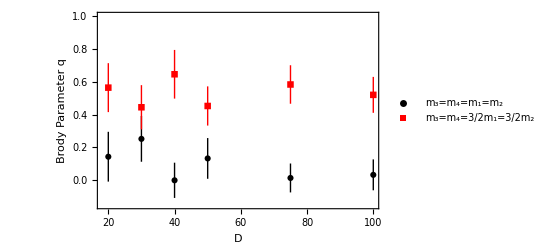

```mathematica
ListPlot[BrodyTable,PlotTheme->None,PlotStyle->{Black,Red},FrameLabel->{"D","Brody Parameter q"},PlotMarkers->Automatic,Frame->True,GridLines->None,GridLinesStyle->Thin,PlotRange->{-0.15,1.0},PlotLegends->Placed[{"m_3=m_4=m_1=m_2","m_3=m_4=3/2m_1=3/2m_2"},{.75,0.85}],LabelStyle->Medium]
```

```mathematica
-248.2
```

-248.2

```mathematica
-248.2/(-2.7 100)
```

0.919259

```mathematica
SVDrhodat4=Table[{√SVDType1Data[[i,1]],SVDType4Data[[i,3]]},{i,1,Length[SVDType4Data]}]
SVDQMdosline4=Fit[SVDrhodat4,{0,x},x]
Show[Plot[SVDQMdosline4,{x,0,√100}],ListPlot[SVDrhodat4]]
```

{{4.47214,4.8003},{5.47723,6.04938},{6.32456,6.68791},{7.07107,7.44403},{8.66025,9.28638},{10.,10.6483}}

0.+1.06807 x

-Graphics-

```mathematica
SVDresults=Show[Plot[{(*SVDQMdosline1,*)SVDQMdosline3,SVDQMdosline4},{x,0,√100},PlotStyle->{{Red,Dashed},{Black,Dashed}},PlotRange->{0,12}],Plot[{(*0.4x,*)0.8x,1.06x},{x,0,√100},PlotRange->{0,12},PlotTheme->None,PlotStyle->{{Red,Thick},{Black,Thick}}],(*ListPlot[SVDrhodat1,PlotMarkers-> "OpenMarkers"],ListPlot[SVDrhodat2,PlotMarkers-> "OpenMarkers"],*)ListPlot[SVDrhodat3,PlotMarkers->"OpenMarkers"],ListPlot[SVDrhodat4,PlotMarkers-> "OpenMarkers"],FrameLabel->{"√D","ρ(E/D = -2.7)"},Frame->True,GridLines->None,GridLinesStyle->Thin,LabelStyle->Medium,Epilog->{Text[Style["ρ_4 = 0.8 r_0^3 √D",12],{4.5,2}],Text[Style["ρ_4 = 1.06 r_0^3 √D",Medium],{5,8}],Text[Style["a.",24,Bold],{0.75,9.5}]},PlotRangeClipping->False,ImageSize->{340,250},
ImagePadding->{{100,20},{50,8}},
AspectRatio->aspctratio,ImageMargins->0,PlotRange->{0,12}]
```

-Graphics-

```mathematica
pscaling=Grid[{{SVDresults,pr0scaling}},Spacings->0]
```

-Graphics- | pr0scaling

```mathematica
Export["/Users/niravmehta/Documents/MyPapers/Molecules-Resubmit-Round1-2020/pscaling.pdf",pscaling]
```

/Users/niravmehta/Documents/MyPapers/Molecules-Resubmit-Round1-2020/pscaling.pdf

```mathematica
Newrun100paths={"/Users/niravmehta/Documents/GitHub/4BodySVD/runs100-8-4-20/run1/","/Users/niravmehta/Documents/GitHub/4BodySVD/runs100-8-4-20/run2/","/Users/niravmehta/Documents/GitHub/4BodySVD/runs100-8-4-20/run3/","/Users/niravmehta/Documents/GitHub/4BodySVD/runs100-8-4-20/run4/"}
```

{/Users/niravmehta/Documents/GitHub/4BodySVD/runs100-8-4-20/run1/,/Users/niravmehta/Documents/GitHub/4BodySVD/runs100-8-4-20/run2/,/Users/niravmehta/Documents/GitHub/4BodySVD/runs100-8-4-20/run3/,/Users/niravmehta/Documents/GitHub/4BodySVD/runs100-8-4-20/run4/}

```mathematica
Table[Analyze[Newrun100paths[[i]],30,bins,bFit,"4BodySVD.par"],{i,1,4}]
```

{{100.,112,3.74864,0.387603,0.0998083,-Graphics-,-Graphics-,-270.},{100.,129,4.3566,0.302962,0.0893402,-Graphics-,-Graphics-,-270.},{100.,242,8.09929,0.122992,0.0566861,-Graphics-,-Graphics-,-270.},{100.,324,10.8506,0.518318,0.0631931,-Graphics-,-Graphics-,-270.}}